```mathematica
(* Propagación de una onda plana limitada por una abertura hasta el plano de Fourier o plano focal de la lente objetivo *)
```

```mathematica
U1 = (2π ⅇ^(ⅈ π λ f ρ^2))/(ⅈ λ f)∫_0^a r BesselJ[0,2π r ρ] ⅆ r
```

-(ⅈ a ⅇ^(ⅈ f π λ ρ^2) BesselJ[1,2 a π ρ])/(f λ ρ)

```mathematica
(* usando identidades de Bessel, libro Goodman, pag. 16  se resuelve la integral *)
```

```mathematica
U1 = (2π ⅇ^(ⅈ π λ f ρ^2))/(ⅈ λ f)a^2∫_0^1 r BesselJ[0,2π a r ρ] ⅆ r
```

```mathematica
U1 = (ⅇ^(ⅈ π λ f ρ^2))/(ⅈ λ f ρ)a BesselJ[1,2π a ρ]
```

```mathematica
(* ρ es la variable de frecuencia, cambiando a la variable espacial R tenemos *)
```

```mathematica
U1 = (ⅇ^(ⅈ π/(λ f) R^2))/(ⅈ R)a BesselJ[1,2π a R/(λ f)]
```

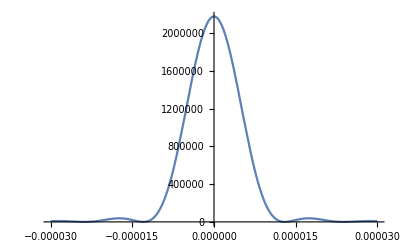

```mathematica
λ = 532*10^-9;
f = 400*10^-3;
a = 10*10^-3;
Plot[Abs[(ⅇ^(ⅈ π/(λ f) R^2))/(ⅈ R)a BesselJ[1,2π a R/(λ f)]]^2,{R,-2*15*10^-6,2*15*10^-6}]
```